```mathematica
eq1 = x'[t] == Cos[x[t]];
eq2 = y'[t] == Cos[y[t]];
```

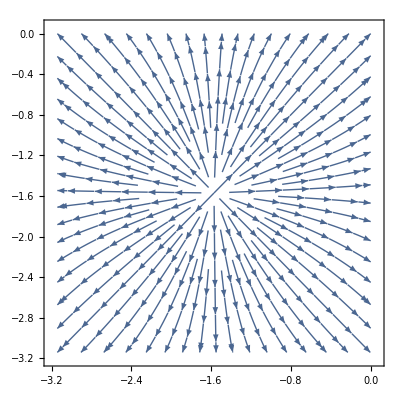

```mathematica
StreamPlot[{Cos[x], Cos[y]},{x,-π, 0}, {y, -π, 0}]
```

```mathematica
(*Очевидное решение уравнения dy/dx=Cos[y]/Cos[x]: ∫ⅆx/Cos[x] - ∫ⅆy/Cos[y]  = Const*)
```

```mathematica
answ = Integrate[1/Cos[x], x]  - Integrate[1/Cos[y], y] // Simplify
```

-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]+Log[Cos[y/2]-Sin[y/2]]-Log[Cos[y/2]+Sin[y/2]]

```mathematica
(*Решение в виде 
Log[Abs[(Cos[x/2]+Sin[x/2])/(Cos[x/2]-Sin[x/2])*(Cos[y/2]-Sin[y/2])/(Cos[y/2]+Sin[y/2])]]=C*)
```

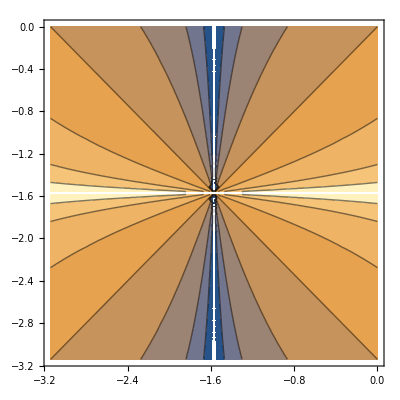

```mathematica
ContourPlot[Log[Abs[(Cos[x/2]+Sin[x/2])/(Cos[x/2]-Sin[x/2])*(Cos[y/2]-Sin[y/2])/(Cos[y/2]+Sin[y/2])]],{x,-π, 0}, {y, -π, 0}]
```

```mathematica
(*Точка покоя в [-π, 0]×[-π, 0], когда Cos[x]=Cos[y]=0: Subscript[x, 0]=-π/2, Subscript[y, 0]=-π/2*)
```

```mathematica
(*Очевидные изоклины: y=-π/2; x=-π/2; y=x-π/2; y=-x-π/2;*)
```

```mathematica
(*Линеаризованную систему уравнений в окрестности особой точки и напишем линейную её часть матричной форме*)
(*x[t] = Subscript[x, 0] + Subscript[u, 1][t], y[t] = Subscript[y, 0] + Subscript[u, 2][t]*)
```

```mathematica
d/dt({{u1}, {u2}})=A ({{u1}, {u2}})
```

```mathematica
A=({{1, 0}, {0, 1}});
```

```mathematica
Eigensystem[A]
```

{{1,1},{{0,1},{1,0}}}

```mathematica
(*Системе получили 2 линейно независымых корня*)
```

```mathematica
Решение системы в окрестности точки покоя будет
```

```mathematica
({{u1}, {u2}})=С1 * ({{1}, {0}})ⅇ^t + C2 * ({{0}, {1}}) ⅇ^t
```

```mathematica
DSolve[{eq1, eq2},{x[t],y[t]},t]
```

{{x[t]→2 ArcTan[Tanh[1/2 (t+C[1])]],y[t]→2 ArcTan[Tanh[1/2 (t+C[2])]]}}